# xCellerator Example

## Six variable mitotic oscillator, Tyson (1991) model

reference: "Modeling the cell division cycle: cdc2 and cyclin interactions"
Proc. Natl. Acad. Sci., USA, 88:7328-7332 (1991)

In the following notebook, we refer to u as aMPF (for active MPF) and z as pMPF (for pre-MPF)

xCellerator implementation
Created: 12 Aug 2005 BES
Revised: 15 Oct 2007 Verify for Mathematica 6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:44:16.145924 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

```mathematica
stn={{M->C2+YP,k6},{C2⇄CP,k8notP,k9},{CP+Y->pM,k3},{M->pM,k5notP},{∅⇄Y,k1aa,k2},{YP->∅,k7},{pM->M, k4prime+k4 M[t]^2}}
```

{{M→C2+YP,k6},{C2⇄CP,k8notP,k9},{CP+Y→pM,k3},{M→pM,k5notP},{∅⇄Y,k1aa,k2},{YP→∅,k7},{pM→M,k4prime+k4 M[t]^2}}

```mathematica
r={k1aa-> .015,k2-> 0, k3-> 200, k4-> 180, k4prime-> 0.018, k5notP-> 0, k6-> 1, k7-> 0.6, k8notP->10^6 , k9-> 1000}
```

{k1aa→0.015,k2→0,k3→200,k4→180,k4prime→0.018,k5notP→0,k6→1,k7→0.6,k8notP→1000000,k9→1000}

```mathematica
s=interpret[stn][[1]]//TableForm
```

C2'[t]==-k8notP C2[t]+k9 CP[t]+k6 M[t]
CP'[t]==k8notP C2[t]-k9 CP[t]-k3 CP[t] Y[t]
M'[t]==-k5notP M[t]-k6 M[t]+(k4prime+k4 M[t]^2) pM[t]
pM'[t]==k5notP M[t]-(k4prime+k4 M[t]^2) pM[t]+k3 CP[t] Y[t]
Y'[t]==k1aa-k2 Y[t]-k3 CP[t] Y[t]
YP'[t]==k6 M[t]-k7 YP[t]

```mathematica
ics={CP-> 1,pM-> .3};
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {C2,M,Y,YP}

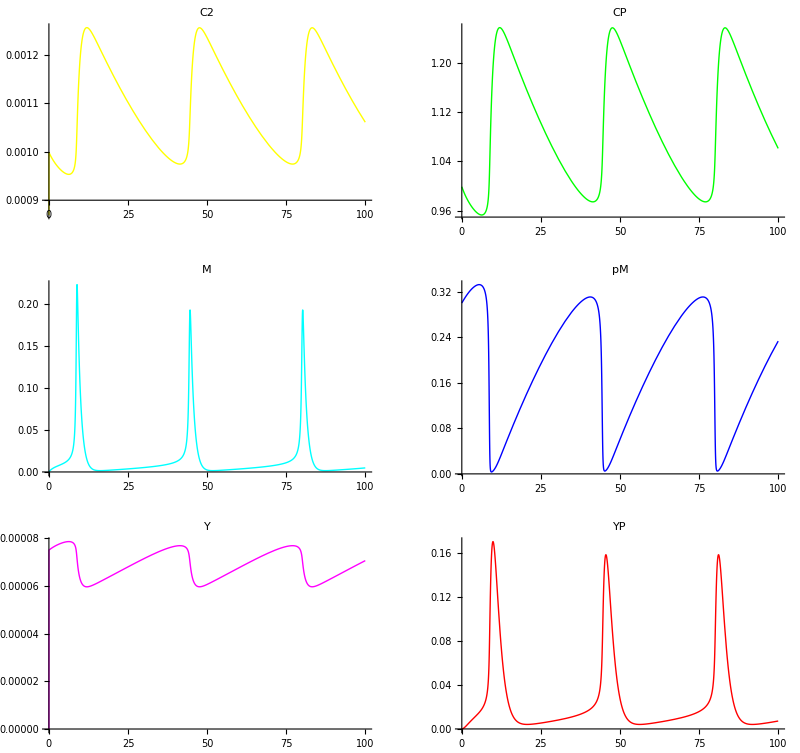

{{C2→InterpolatingFunction[{{0.,100.}},<>],CP→InterpolatingFunction[{{0.,100.}},<>],M→InterpolatingFunction[{{0.,100.}},<>],pM→InterpolatingFunction[{{0.,100.}},<>],Y→InterpolatingFunction[{{0.,100.}},<>],YP→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
n=run[stn,
rates-> r,
initialConditions-> ics,plotColumns-> 2,
gridPlotVariables-> All,plotVariables-> None, plot-> True]
```

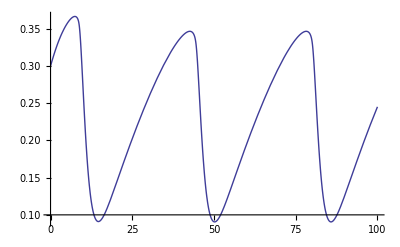

```mathematica
Plot[(YP[t]+Y[t]+pM[t]+M[t])/.n, {t,0,100}]
```

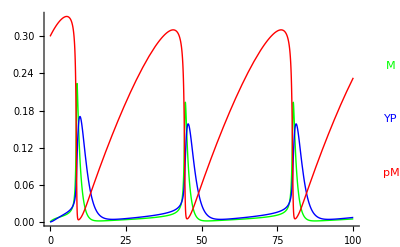

```mathematica
runPlot[n, {M, YP, pM}]
```